What we need for constructing the 3 D phase plot :
 1) Define the dynamical system
 2) Solve for fixed points (will be used in labelling these points in the plots for aesthetics)
 3) Define an ODE solver to solve the system with the given initial conditions (will be used to highlight some curves/trajectories/solutions in the plot)
 4) Plot the other relevant regions and trajectories
 5) Overlay the trajectories, labels of the fixed point, highlighted regions onto the constructed 3D vector plot

### Dynamical system

Defining the dynamical system, we have the following differential equations :

```mathematica
λ=1+2/10;ϵ=1+9/10;(*P19 is stable node, P2 is unstable node*)(*done*)
```

```mathematica
Dx[x_,y_,s_] := √(3/2)λ y^2 - 3x + x (1 + 2 x^2 - y^2 + 1/2 s^2)-1/(2 x)ϵ(x^2+y^2)s^2
Dy[x_,y_,s_]:=-√(3/2)λ x y +y (1 + 2 x^2 - y^2 + 1/2 s^2)
Ds[x_,y_,s_]:=s(1/2 ϵ(x^2+y^2)-1/2+2 x^2 - y^2 + 1/2 s^2)
```

Note that the plane x = 0 is undefined in this system

### Fixed points

Solving for the fixed points,

```mathematica
Solve[{Dx[x,y,s]==0,Dy[x,y,s]==0,Ds[x,y,s]==0},{x,y,s}]
```

{{x→-1,y→0,s→0},{x→-1/2,y→0,s→-ⅈ},{x→-1/2,y→0,s→ⅈ},{x→1/2,y→0,s→-ⅈ},{x→1/2,y→0,s→ⅈ},{x→1,y→0,s→0},{x→√(2/3),y→-1/2 ⅈ √(5/3),s→-ⅈ √(7/2)},{x→√(2/3),y→-1/2 ⅈ √(5/3),s→ⅈ √(7/2)},{x→√(2/3),y→1/2 ⅈ √(5/3),s→-ⅈ √(7/2)},{x→√(2/3),y→1/2 ⅈ √(5/3),s→ⅈ √(7/2)},{x→√(2/3),y→-2/(√3),s→0},{x→√(2/3),y→2/(√3),s→0},{x→1/(√6),y→-√(5/6),s→0},{x→1/(√6),y→√(5/6),s→0},{x→1/48 (√6-ⅈ √282),y→-1/8 (-1)^(1/4) √(7/3 (-23 ⅈ+√47)),s→-1/4 (-1)^(3/4) √(1/2 (9 ⅈ+√47))},{x→1/48 (√6-ⅈ √282),y→-1/8 (-1)^(1/4) √(7/3 (-23 ⅈ+√47)),s→1/4 (-1)^(3/4) √(1/2 (9 ⅈ+√47))},{x→1/48 (√6-ⅈ √282),y→1/8 (-1)^(1/4) √(7/3 (-23 ⅈ+√47)),s→-1/4 (-1)^(3/4) √(1/2 (9 ⅈ+√47))},{x→1/48 (√6-ⅈ √282),y→1/8 (-1)^(1/4) √(7/3 (-23 ⅈ+√47)),s→1/4 (-1)^(3/4) √(1/2 (9 ⅈ+√47))},{x→1/48 (√6+ⅈ √282),y→-1/8 (-1)^(3/4) √(7/3 (23 ⅈ+√47)),s→-((-1)^(1/4) √(-9 ⅈ+√47))/(4 √2)},{x→1/48 (√6+ⅈ √282),y→-1/8 (-1)^(3/4) √(7/3 (23 ⅈ+√47)),s→((-1)^(1/4) √(-9 ⅈ+√47))/(4 √2)},{x→1/48 (√6+ⅈ √282),y→1/8 (-1)^(3/4) √(7/3 (23 ⅈ+√47)),s→-((-1)^(1/4) √(-9 ⅈ+√47))/(4 √2)},{x→1/48 (√6+ⅈ √282),y→1/8 (-1)^(3/4) √(7/3 (23 ⅈ+√47)),s→((-1)^(1/4) √(-9 ⅈ+√47))/(4 √2)}}

### Fixed points (in general form)

In general, the fixed points of the given dynamical system have the form :

```mathematica
FPgen={{x->-1,y->0,s->0},{x->1,y->0,s->0},{x->-1/(√ϵ),y->0,s->-(2 ⅈ)/(√ϵ)},{x->-1/(√ϵ),y->0,s->(2 ⅈ)/(√ϵ)},{x->1/(√ϵ),y->0,s->-(2 ⅈ)/(√ϵ)},{x->1/(√ϵ),y->0,s->(2 ⅈ)/(√ϵ)},{x->(√(2/3))/λ,y->-2/(√3 λ),s->0},{x->(√(2/3))/λ,y->2/(√3 λ),s->0},{x->(√(2/3))/λ,y->-(√(3-(2 ϵ)/λ^2))/(√3 √ϵ),s->-(√2 √(-2 ϵ+λ^2))/(√ϵ λ)},{x->(√(2/3))/λ,y->-(√(3-(2 ϵ)/λ^2))/(√3 √ϵ),s->(√2 √(-2 ϵ+λ^2))/(√ϵ λ)},{x->(√(2/3))/λ,y->(√(3-(2 ϵ)/λ^2))/(√3 √ϵ),s->-(√2 √(-2 ϵ+λ^2))/(√ϵ λ)},{x->(√(2/3))/λ,y->(√(3-(2 ϵ)/λ^2))/(√3 √ϵ),s->(√2 √(-2 ϵ+λ^2))/(√ϵ λ)},{x->λ/(√6),y->-(√(6-λ^2))/(√6),s->0},{x->λ/(√6),y->(√(6-λ^2))/(√6),s->0},{x->(-6 λ+2 ϵ λ-2 √(36 ϵ-12 ϵ^2+9 λ^2-6 ϵ λ^2+ϵ^2 λ^2))/(4 √6 ϵ),y->-1/(2 √3 √ϵ)(√(18+6 ϵ+(9 λ^2)/ϵ-ϵ λ^2+λ √(36 ϵ-12 ϵ^2+9 λ^2-6 ϵ λ^2+ϵ^2 λ^2)+(3 λ √(36 ϵ-12 ϵ^2+9 λ^2-6 ϵ λ^2+ϵ^2 λ^2))/ϵ)),s->-(√(-6+2 ϵ+λ^2-(3 λ^2)/ϵ-(λ √(36 ϵ-12 ϵ^2+9 λ^2-6 ϵ λ^2+ϵ^2 λ^2))/ϵ))/(√2 √ϵ)},{x->(-6 λ+2 ϵ λ-2 √(36 ϵ-12 ϵ^2+9 λ^2-6 ϵ λ^2+ϵ^2 λ^2))/(4 √6 ϵ),y->-1/(2 √3 √ϵ)(√(18+6 ϵ+(9 λ^2)/ϵ-ϵ λ^2+λ √(36 ϵ-12 ϵ^2+9 λ^2-6 ϵ λ^2+ϵ^2 λ^2)+(3 λ √(36 ϵ-12 ϵ^2+9 λ^2-6 ϵ λ^2+ϵ^2 λ^2))/ϵ)),s->(√(-6+2 ϵ+λ^2-(3 λ^2)/ϵ-(λ √(36 ϵ-12 ϵ^2+9 λ^2-6 ϵ λ^2+ϵ^2 λ^2))/ϵ))/(√2 √ϵ)},{x->(-6 λ+2 ϵ λ-2 √(36 ϵ-12 ϵ^2+9 λ^2-6 ϵ λ^2+ϵ^2 λ^2))/(4 √6 ϵ),y->1/(2 √3 √ϵ)(√(18+6 ϵ+(9 λ^2)/ϵ-ϵ λ^2+λ √(36 ϵ-12 ϵ^2+9 λ^2-6 ϵ λ^2+ϵ^2 λ^2)+(3 λ √(36 ϵ-12 ϵ^2+9 λ^2-6 ϵ λ^2+ϵ^2 λ^2))/ϵ)),s->-(√(-6+2 ϵ+λ^2-(3 λ^2)/ϵ-(λ √(36 ϵ-12 ϵ^2+9 λ^2-6 ϵ λ^2+ϵ^2 λ^2))/ϵ))/(√2 √ϵ)},{x->(-6 λ+2 ϵ λ-2 √(36 ϵ-12 ϵ^2+9 λ^2-6 ϵ λ^2+ϵ^2 λ^2))/(4 √6 ϵ),y->1/(2 √3 √ϵ)(√(18+6 ϵ+(9 λ^2)/ϵ-ϵ λ^2+λ √(36 ϵ-12 ϵ^2+9 λ^2-6 ϵ λ^2+ϵ^2 λ^2)+(3 λ √(36 ϵ-12 ϵ^2+9 λ^2-6 ϵ λ^2+ϵ^2 λ^2))/ϵ)),s->(√(-6+2 ϵ+λ^2-(3 λ^2)/ϵ-(λ √(36 ϵ-12 ϵ^2+9 λ^2-6 ϵ λ^2+ϵ^2 λ^2))/ϵ))/(√2 √ϵ)},{x->(-6 λ+2 ϵ λ+2 √(36 ϵ-12 ϵ^2+9 λ^2-6 ϵ λ^2+ϵ^2 λ^2))/(4 √6 ϵ),y->-1/(2 √3 √ϵ)(√(18+6 ϵ+(9 λ^2)/ϵ-ϵ λ^2-λ √(36 ϵ-12 ϵ^2+9 λ^2-6 ϵ λ^2+ϵ^2 λ^2)-(3 λ √(36 ϵ-12 ϵ^2+9 λ^2-6 ϵ λ^2+ϵ^2 λ^2))/ϵ)),s->-(√(-6+2 ϵ+λ^2-(3 λ^2)/ϵ+(λ √(36 ϵ-12 ϵ^2+9 λ^2-6 ϵ λ^2+ϵ^2 λ^2))/ϵ))/(√2 √ϵ)},{x->(-6 λ+2 ϵ λ+2 √(36 ϵ-12 ϵ^2+9 λ^2-6 ϵ λ^2+ϵ^2 λ^2))/(4 √6 ϵ),y->-1/(2 √3 √ϵ)(√(18+6 ϵ+(9 λ^2)/ϵ-ϵ λ^2-λ √(36 ϵ-12 ϵ^2+9 λ^2-6 ϵ λ^2+ϵ^2 λ^2)-(3 λ √(36 ϵ-12 ϵ^2+9 λ^2-6 ϵ λ^2+ϵ^2 λ^2))/ϵ)),s->(√(-6+2 ϵ+λ^2-(3 λ^2)/ϵ+(λ √(36 ϵ-12 ϵ^2+9 λ^2-6 ϵ λ^2+ϵ^2 λ^2))/ϵ))/(√2 √ϵ)},{x->(-6 λ+2 ϵ λ+2 √(36 ϵ-12 ϵ^2+9 λ^2-6 ϵ λ^2+ϵ^2 λ^2))/(4 √6 ϵ),y->1/(2 √3 √ϵ)(√(18+6 ϵ+(9 λ^2)/ϵ-ϵ λ^2-λ √(36 ϵ-12 ϵ^2+9 λ^2-6 ϵ λ^2+ϵ^2 λ^2)-(3 λ √(36 ϵ-12 ϵ^2+9 λ^2-6 ϵ λ^2+ϵ^2 λ^2))/ϵ)),s->-(√(-6+2 ϵ+λ^2-(3 λ^2)/ϵ+(λ √(36 ϵ-12 ϵ^2+9 λ^2-6 ϵ λ^2+ϵ^2 λ^2))/ϵ))/(√2 √ϵ)},{x->(-6 λ+2 ϵ λ+2 √(36 ϵ-12 ϵ^2+9 λ^2-6 ϵ λ^2+ϵ^2 λ^2))/(4 √6 ϵ),y->1/(2 √3 √ϵ)(√(18+6 ϵ+(9 λ^2)/ϵ-ϵ λ^2-λ √(36 ϵ-12 ϵ^2+9 λ^2-6 ϵ λ^2+ϵ^2 λ^2)-(3 λ √(36 ϵ-12 ϵ^2+9 λ^2-6 ϵ λ^2+ϵ^2 λ^2))/ϵ)),s->(√(-6+2 ϵ+λ^2-(3 λ^2)/ϵ+(λ √(36 ϵ-12 ϵ^2+9 λ^2-6 ϵ λ^2+ϵ^2 λ^2))/ϵ))/(√2 √ϵ)}}//MatrixForm
```

(x→-1 | y→0 | s→0
x→1 | y→0 | s→0
x→-√(10/19) | y→0 | s→-2 ⅈ √(10/19)
x→-√(10/19) | y→0 | s→2 ⅈ √(10/19)
x→√(10/19) | y→0 | s→-2 ⅈ √(10/19)
x→√(10/19) | y→0 | s→2 ⅈ √(10/19)
x→5/(3 √6) | y→-5/(3 √3) | s→0
x→5/(3 √6) | y→5/(3 √3) | s→0
x→5/(3 √6) | y→-(√(65/114))/3 | s→-1/3 ⅈ √(295/19)
x→5/(3 √6) | y→-(√(65/114))/3 | s→1/3 ⅈ √(295/19)
x→5/(3 √6) | y→(√(65/114))/3 | s→-1/3 ⅈ √(295/19)
x→5/(3 √6) | y→(√(65/114))/3 | s→1/3 ⅈ √(295/19)
x→(√6)/5 | y→-(√19)/5 | s→0
x→(√6)/5 | y→(√19)/5 | s→0
x→(5 (-66/25-(4 √4191)/25))/(38 √6) | y→-√(5/114 (79527/2375+(588 √4191)/2375)) | s→-ⅈ √(5/19 (1441/475+(24 √4191)/475))
x→(5 (-66/25-(4 √4191)/25))/(38 √6) | y→-√(5/114 (79527/2375+(588 √4191)/2375)) | s→ⅈ √(5/19 (1441/475+(24 √4191)/475))
x→(5 (-66/25-(4 √4191)/25))/(38 √6) | y→√(5/114 (79527/2375+(588 √4191)/2375)) | s→-ⅈ √(5/19 (1441/475+(24 √4191)/475))
x→(5 (-66/25-(4 √4191)/25))/(38 √6) | y→√(5/114 (79527/2375+(588 √4191)/2375)) | s→ⅈ √(5/19 (1441/475+(24 √4191)/475))
x→(5 (-66/25+(4 √4191)/25))/(38 √6) | y→-√(5/114 (79527/2375-(588 √4191)/2375)) | s→-√(5/19 (-1441/475+(24 √4191)/475))
x→(5 (-66/25+(4 √4191)/25))/(38 √6) | y→-√(5/114 (79527/2375-(588 √4191)/2375)) | s→√(5/19 (-1441/475+(24 √4191)/475))
x→(5 (-66/25+(4 √4191)/25))/(38 √6) | y→√(5/114 (79527/2375-(588 √4191)/2375)) | s→-√(5/19 (-1441/475+(24 √4191)/475))
x→(5 (-66/25+(4 √4191)/25))/(38 √6) | y→√(5/114 (79527/2375-(588 √4191)/2375)) | s→√(5/19 (-1441/475+(24 √4191)/475)))

### Numerically solving the ODE

Here, we define an ODE solver with the given rules for increasing precision to numerically solve the system

```mathematica
rules={AccuracyGoal-> Infinity,PrecisionGoal-> 25, WorkingPrecision-> 50, MaxSteps->50000};
```

```mathematica
ODE[x0_,y0_,s0_]:=NDSolve[{x'[t]==Dx[x[t],y[t],s[t]],y'[t]==Dy[x[t],y[t],s[t]],s'[t]==Ds[x[t],y[t],s[t]], x[0]==x0, y[0]==y0,s[0]==s0}, {x,y,s},{t,0,100},Method->"StiffnessSwitching", rules];
```

#### Trajectories for the whole phase plot (w/o x→0): λ = 1.2, ϵ=1.9

```mathematica
solW[15]=ODE[1-(2/1000-(8/10000+2/100000)),-5/100,-5/100000];
```

```mathematica
solW[14]=ODE[1-(2/1000-(8/10000+2/100000)),5/100,-5/100000];
```

```mathematica
solW[13]=ODE[1-(2/1000-(8/10000+2/100000)),-5/100,5/100000];
```

```mathematica
solW[12]=ODE[1-5/10000,-1/100,-5/1000];
```

```mathematica
solW[11]=ODE[1-5/10000,1/100,-5/1000];
```

```mathematica
solW[10]=ODE[1-5/10000,-1/100,5/1000];
```

```mathematica
solW[9]=ODE[1-(5/100000-(1/1000000+5/10000000)),-1/100,-1/10000];
```

```mathematica
solW[8]=ODE[1-(5/100000-(1/1000000+5/10000000)),1/100,-1/10000];
```

```mathematica
solW[7]=ODE[1-(5/100000-(1/1000000+5/10000000)),-1/100,1/10000];
```

```mathematica
solW[6]=ODE[1-(1/10000-(5/100000+1/1000000)),1/100,1/10000];
```

```mathematica
solW[5]=ODE[1-(1/10000-(5/100000)),1/100,5/10000];
```

```mathematica
solW[4]=ODE[1-7/100000,1/100,1/1000];
```

```mathematica
solW[3]=ODE[1-(2/1000-(8/10000+2/100000)),5/100,5/100000];
```

```mathematica
solW[2]=ODE[1-(5/100000-(1/1000000+5/10000000)),1/100,1/10000];
```

```mathematica
solW[1]=ODE[1-5/10000,1/100,5/1000];
```

#### Possible trajectories for the first quadrant phase plot (w/o x→0): λ = 1.2, ϵ=1.9

```mathematica
sol[1]=ODE[1-5/10000,1/100,5/1000];
```

```mathematica
sol[2]=ODE[1-(5/100000-(1/1000000+5/10000000)),1/100,1/10000];
```

```mathematica
sol[3]=ODE[1-(2/1000-(8/10000+2/100000)),5/100,5/100000];
```

```mathematica
sol[4]=ODE[8/10,1/100,1/100];
```

```mathematica
sol[5]=ODE[1-4/100,3/10,1/1000];
```

```mathematica
sol[6]=ODE[1-2/100,2/10,1/1000];
```

```mathematica
sol[7]=ODE[1-2/10,1+4/10,1/1000];
```

NDSolve::ndsz: At t == 0.80430695581540256655672873535265511187822812961344, step size is effectively zero; singularity or stiff system suspected.

```mathematica
sol[8]=ODE[1-4/10,1+4/10,1/1000];
```

NDSolve::ndsz: At t == 1.5324684268512132393453173613437061527177314780912, step size is effectively zero; singularity or stiff system suspected.

```mathematica
sol[9]=ODE[1-6/10,1+4/10,1/1000];
```

NDSolve::ndsz: At t == 3.9577622169872202007738285873269653499539392339798, step size is effectively zero; singularity or stiff system suspected.

```mathematica
sol[10]=ODE[1/100,1+4/10,1/1000];
```

```mathematica
sol[11]=ODE[1/100,1+7/10,1/10];
```

```mathematica
sol[12]=ODE[1-9/10,1+4/10,3/10];
```

```mathematica
sol[13]=ODE[1-9/10,1+4/10,2/10];
```

```mathematica
sol[14]=ODE[5/100,1+5/10,2/10];
```

```mathematica
sol[15]=ODE[5/100,1+5/10,1/10];
```

```mathematica
sol[16]=ODE[5/10,1+4/10+9/100,1/10+7/100];
```

NDSolve::ndsz: At t == 2.1278897098030688563211586393096560620642765386758, step size is effectively zero; singularity or stiff system suspected.

```mathematica
sol[17]=ODE[5/10,1+4/10+9/100,1/100];
```

NDSolve::ndsz: At t == 1.8609116259548605343459984747590560687529773275197, step size is effectively zero; singularity or stiff system suspected.

```mathematica
sol[18]=ODE[5/10,1+5/10,5/10];
```

NDSolve::ndsz: At t == 1.1407373146982140410947189815565588353824329577711, step size is effectively zero; singularity or stiff system suspected.

```mathematica
sol[19]=ODE[2/1000,5/10,3/100];
```

```mathematica
sol[20]=ODE[2/1000,9/10,3/100];
```

```mathematica
sol[21]=ODE[5/100,5/10,1/10+5/100];
```

```mathematica
sol[22]=ODE[9/10,3/10,1/10+5/100];
```

```mathematica
sol[23]=ODE[3/10,3/10,1/10+5/100];
```

```mathematica
sol[24]=ODE[3/10,3/10,5/10];
```

NDSolve::ndsz: At t == 0.72119678822786537153053118350344002701910986378726, step size is effectively zero; singularity or stiff system suspected.

```mathematica
sol[25]=ODE[7/10,3/10,3/10];
```

```mathematica
sol[26]=ODE[7/10,1/10,3/10];
```

```mathematica
sol[27]=ODE[7/10,1/10,1/10];
```

```mathematica
sol[28]=ODE[7/10,1/10,6/10];
```

NDSolve::ndsz: At t == 1.0087497307671440082305569367022844753539766996076, step size is effectively zero; singularity or stiff system suspected.

```mathematica
sol[29]=ODE[10/10,1/100,1/10];
```

NDSolve::ndsz: At t == 1.690233241268889237787179640941726540800492342194, step size is effectively zero; singularity or stiff system suspected.

```mathematica
sol[30]=ODE[9/10,1/100,1/10];
```

```mathematica
sol[31]=ODE[8/10,1/100,5/10];
```

NDSolve::ndsz: At t == 1.7944074335281784053618623868613250407047863331553, step size is effectively zero; singularity or stiff system suspected.

```mathematica
sol[32]=ODE[8/10,5/10,5/10];
```

NDSolve::ndsz: At t == 0.75337650901405060595799502630086986204364023253271, step size is effectively zero; singularity or stiff system suspected.

```mathematica
sol[33]=ODE[9/10+5/100,5/10,1/100];
```

NDSolve::ndsz: At t == 1.1862699988831636932928036148138029739432944182951, step size is effectively zero; singularity or stiff system suspected.

```mathematica
sol[34]=ODE[9/10+5/100,5/10,1/1000];
```

NDSolve::ndsz: At t == 1.1774527643599962436126526314311078565519548332126, step size is effectively zero; singularity or stiff system suspected.

```mathematica
sol[35]=ODE[9/10,9/10,1/100000];
```

NDSolve::ndsz: At t == 0.87771533914015700920655530455331109610675977083344, step size is effectively zero; singularity or stiff system suspected.

```mathematica
sol[36]=ODE[1/100,1+3/10,7/100+7/1000];
```

#### Gray trajectories (those that approach x=0)

```mathematica
solG[1]=ODE[5/10,1+5/10,5/10];
```

NDSolve::ndsz: At t == 1.1407373146982140410947189815565588353824329577711, step size is effectively zero; singularity or stiff system suspected.

```mathematica
solG[2]=ODE[3/10,3/10,5/10];
```

NDSolve::ndsz: At t == 0.72119678822786537153053118350344002701910986378726, step size is effectively zero; singularity or stiff system suspected.

```mathematica
solG[3]=ODE[8/10,1/100,5/10];
```

NDSolve::ndsz: At t == 1.7944074335281784053618623868613250407047863331553, step size is effectively zero; singularity or stiff system suspected.

```mathematica
solG[4]=ODE[8/10,5/10,5/10];
```

NDSolve::ndsz: At t == 0.75337650901405060595799502630086986204364023253271, step size is effectively zero; singularity or stiff system suspected.

```mathematica
solG[5]=ODE[1+1/100000,1/100,1/100];
```

NDSolve::ndsz: At t == 2.4568323862353315885197724481240297010209337788674, step size is effectively zero; singularity or stiff system suspected.

```mathematica
solG[6]=ODE[5/10,1+4/10+9/100,7/100];
```

NDSolve::ndsz: At t == 2.105176508872910459855040192421943602012957405168, step size is effectively zero; singularity or stiff system suspected.

```mathematica
solG[7]=ODE[1-(1/10000-(5/100000+1/1000000)),1/100,1/10000];
```

```mathematica
solG[8]=ODE[1-(1/10000-(5/100000)),1/100,5/10000];
```

```mathematica
solG[9]=ODE[1-7/100000,1/100,1/1000];
```

### Points (for the first quadrant phase plot)

For aesthetics, we indicate the location of the fixed points in the plots and label them (need to first run fixed points (in general form) section).

```mathematica
Point1=Graphics3D[{PointSize->Large,Point[{{x/.N[FPgen⟦1,1,1⟧],y/.N[FPgen⟦1,1,2⟧],s/.N[FPgen⟦1,1,3⟧]}}]},PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point1Label=Graphics3D[Text[Style["A",Medium,FontWeight->Bold],{0.1+x/.N[FPgen⟦1,1,1⟧],0.1+y/.N[FPgen⟦1,1,2⟧],0.1+s/.N[FPgen⟦1,1,3⟧]}],PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point2=Graphics3D[{PointSize->Large,Point[{{x/.N[FPgen⟦1,2,1⟧],y/.N[FPgen⟦1,2,2⟧],s/.N[FPgen⟦1,2,3⟧]}}]},PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point2Label=Graphics3D[Text[Style["B",Medium,FontWeight->Bold],{0.1+x/.N[FPgen⟦1,2,1⟧],0.1+y/.N[FPgen⟦1,2,2⟧],0.1+s/.N[FPgen⟦1,2,3⟧]}],PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point7=Graphics3D[{PointSize->Large,Point[{{x/.N[FPgen⟦1,7,1⟧],y/.N[FPgen⟦1,7,2⟧],s/.N[FPgen⟦1,7,3⟧]}}]},PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point7Label=Graphics3D[Text[Style["C_-",Medium,FontWeight->Bold],{0.1+x/.N[FPgen⟦1,7,1⟧],0.1+y/.N[FPgen⟦1,7,2⟧],0.1+s/.N[FPgen⟦1,7,3⟧]}],PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point8=Graphics3D[{PointSize->Large,Point[{{x/.N[FPgen⟦1,8,1⟧],y/.N[FPgen⟦1,8,2⟧],s/.N[FPgen⟦1,8,3⟧]}}]},PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point8Label=Graphics3D[Text[Style["C_+",Medium,FontWeight->Bold],{0.1+x/.N[FPgen⟦1,8,1⟧],0.1+y/.N[FPgen⟦1,8,2⟧],0.1+s/.N[FPgen⟦1,8,3⟧]}],PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point9=Graphics3D[{PointSize->Large,Point[{{x/.N[FPgen⟦1,9,1⟧],y/.N[FPgen⟦1,9,2⟧],s/.N[FPgen⟦1,9,3⟧]}}]},PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point9Label=Graphics3D[Text[Style["D_-",Medium,FontWeight->Bold],{0.1+x/.N[FPgen⟦1,9,1⟧],0.1+y/.N[FPgen⟦1,9,2⟧],0.1+s/.N[FPgen⟦1,9,3⟧]}],PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point10=Graphics3D[{PointSize->Large,Point[{{x/.N[FPgen⟦1,10,1⟧],y/.N[FPgen⟦1,10,2⟧],s/.N[FPgen⟦1,10,3⟧]}}]},PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point10Label=Graphics3D[Text[Style["D_+",Medium,FontWeight->Bold],{0.1+x/.N[FPgen⟦1,10,1⟧],0.1+y/.N[FPgen⟦1,10,2⟧],0.1+s/.N[FPgen⟦1,10,3⟧]}],PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point11=Graphics3D[{PointSize->Large,Point[{{x/.N[FPgen⟦1,11,1⟧],y/.N[FPgen⟦1,11,2⟧],s/.N[FPgen⟦1,11,3⟧]}}]},PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point11Label=Graphics3D[Text[Style["E_-",Medium,FontWeight->Bold],{0.1+x/.N[FPgen⟦1,11,1⟧],0.1+y/.N[FPgen⟦1,11,2⟧],0.1+s/.N[FPgen⟦1,11,3⟧]}],PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point12=Graphics3D[{PointSize->Large,Point[{{x/.N[FPgen⟦1,12,1⟧],y/.N[FPgen⟦1,12,2⟧],s/.N[FPgen⟦1,12,3⟧]}}]},PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point12Label=Graphics3D[Text[Style["E_+",Medium,FontWeight->Bold],{0.1+x/.N[FPgen⟦1,12,1⟧],0.1+y/.N[FPgen⟦1,12,2⟧],0.1+s/.N[FPgen⟦1,12,3⟧]}],PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point13=Graphics3D[{PointSize->Large,Point[{{x/.N[FPgen⟦1,13,1⟧],y/.N[FPgen⟦1,13,2⟧],s/.N[FPgen⟦1,13,3⟧]}}]},PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point13Label=Graphics3D[Text[Style["F_-",Medium,FontWeight->Bold],{(x/.N[FPgen⟦1,13,1⟧])-0.1,(y/.N[FPgen⟦1,13,2⟧])-0.1,0.1+s/.N[FPgen⟦1,13,3⟧]}],PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point14=Graphics3D[{PointSize->Large,Point[{{x/.N[FPgen⟦1,14,1⟧],y/.N[FPgen⟦1,14,2⟧],s/.N[FPgen⟦1,14,3⟧]}}]},PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point14Label=Graphics3D[Text[Style["F_+",Medium,FontWeight->Bold],{(x/.N[FPgen⟦1,14,1⟧])-0.1,(y/.N[FPgen⟦1,14,2⟧])-0.1,0.1+s/.N[FPgen⟦1,14,3⟧]}],PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point19=Graphics3D[{PointSize->Large,Point[{{x/.N[FPgen⟦1,19,1⟧],y/.N[FPgen⟦1,19,2⟧],s/.N[FPgen⟦1,19,3⟧]}}]},PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point19Label=Graphics3D[Text[Style["G_-",Medium,FontWeight->Bold],{0.1+x/.N[FPgen⟦1,19,1⟧],0.1+y/.N[FPgen⟦1,19,2⟧],0.1+s/.N[FPgen⟦1,19,3⟧]}],PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point20=Graphics3D[{PointSize->Large,Point[{{x/.N[FPgen⟦1,20,1⟧],y/.N[FPgen⟦1,20,2⟧],s/.N[FPgen⟦1,20,3⟧]}}]},PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point20Label=Graphics3D[Text[Style["G_+",Medium,FontWeight->Bold],{0.1+x/.N[FPgen⟦1,20,1⟧],0.1+y/.N[FPgen⟦1,20,2⟧],0.1+s/.N[FPgen⟦1,20,3⟧]}],PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point21=Graphics3D[{PointSize->Large,Point[{{x/.N[FPgen⟦1,21,1⟧],y/.N[FPgen⟦1,21,2⟧],s/.N[FPgen⟦1,21,3⟧]}}]},PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point21Label=Graphics3D[Text[Style["H_-",Medium,FontWeight->Bold],{0.1+x/.N[FPgen⟦1,21,1⟧],0.1+y/.N[FPgen⟦1,21,2⟧],0.1+s/.N[FPgen⟦1,21,3⟧]}],PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point22=Graphics3D[{PointSize->Large,Point[{{x/.N[FPgen⟦1,22,1⟧],y/.N[FPgen⟦1,22,2⟧],s/.N[FPgen⟦1,22,3⟧]}}]},PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point22Label=Graphics3D[Text[Style["H_+",Medium,FontWeight->Bold],{0.1+x/.N[FPgen⟦1,22,1⟧],0.1+y/.N[FPgen⟦1,22,2⟧],0.1+s/.N[FPgen⟦1,22,3⟧]}],PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
```

### Points (for the whole phase plot)

For aesthetics, we indicate the location of the fixed points in the plots and label them (some points have different label positions compared to the first quadrant phase plot for readability)(need to first run fixed points (in general form) section).

```mathematica
Point1W=Graphics3D[{PointSize->Large,Point[{{x/.N[FPgen⟦1,1,1⟧],y/.N[FPgen⟦1,1,2⟧],s/.N[FPgen⟦1,1,3⟧]}}]},PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point1LabelW=Graphics3D[Text[Style["A",Medium,FontWeight->Bold],{0.1+x/.N[FPgen⟦1,1,1⟧],0.1+y/.N[FPgen⟦1,1,2⟧],0.1+s/.N[FPgen⟦1,1,3⟧]}],PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point2W=Graphics3D[{PointSize->Large,Point[{{x/.N[FPgen⟦1,2,1⟧],y/.N[FPgen⟦1,2,2⟧],s/.N[FPgen⟦1,2,3⟧]}}]},PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point2LabelW=Graphics3D[Text[Style["B",Medium,FontWeight->Bold],{0.1+x/.N[FPgen⟦1,2,1⟧],0.1+y/.N[FPgen⟦1,2,2⟧],0.1+s/.N[FPgen⟦1,2,3⟧]}],PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point7W=Graphics3D[{PointSize->Large,Point[{{x/.N[FPgen⟦1,7,1⟧],y/.N[FPgen⟦1,7,2⟧],s/.N[FPgen⟦1,7,3⟧]}}]},PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point7LabelW=Graphics3D[Text[Style["C_-",Medium,FontWeight->Bold],{(x/.N[FPgen⟦1,7,1⟧])-0.1,(y/.N[FPgen⟦1,7,2⟧])-0.1,0.1+s/.N[FPgen⟦1,7,3⟧]}],PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point8W=Graphics3D[{PointSize->Large,Point[{{x/.N[FPgen⟦1,8,1⟧],y/.N[FPgen⟦1,8,2⟧],s/.N[FPgen⟦1,8,3⟧]}}]},PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point8LabelW=Graphics3D[Text[Style["C_+",Medium,FontWeight->Bold],{0.1+x/.N[FPgen⟦1,8,1⟧],0.1+y/.N[FPgen⟦1,8,2⟧],0.1+s/.N[FPgen⟦1,8,3⟧]}],PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point9W=Graphics3D[{PointSize->Large,Point[{{x/.N[FPgen⟦1,9,1⟧],y/.N[FPgen⟦1,9,2⟧],s/.N[FPgen⟦1,9,3⟧]}}]},PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point9LabelW=Graphics3D[Text[Style["D_-",Medium,FontWeight->Bold],{0.1+x/.N[FPgen⟦1,9,1⟧],0.1+y/.N[FPgen⟦1,9,2⟧],0.1+s/.N[FPgen⟦1,9,3⟧]}],PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point10W=Graphics3D[{PointSize->Large,Point[{{x/.N[FPgen⟦1,10,1⟧],y/.N[FPgen⟦1,10,2⟧],s/.N[FPgen⟦1,10,3⟧]}}]},PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point10LabelW=Graphics3D[Text[Style["D_+",Medium,FontWeight->Bold],{0.1+x/.N[FPgen⟦1,10,1⟧],0.1+y/.N[FPgen⟦1,10,2⟧],0.1+s/.N[FPgen⟦1,10,3⟧]}],PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point11W=Graphics3D[{PointSize->Large,Point[{{x/.N[FPgen⟦1,11,1⟧],y/.N[FPgen⟦1,11,2⟧],s/.N[FPgen⟦1,11,3⟧]}}]},PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point11LabelW=Graphics3D[Text[Style["E_-",Medium,FontWeight->Bold],{0.1+x/.N[FPgen⟦1,11,1⟧],0.1+y/.N[FPgen⟦1,11,2⟧],0.1+s/.N[FPgen⟦1,11,3⟧]}],PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point12W=Graphics3D[{PointSize->Large,Point[{{x/.N[FPgen⟦1,12,1⟧],y/.N[FPgen⟦1,12,2⟧],s/.N[FPgen⟦1,12,3⟧]}}]},PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point12LabelW=Graphics3D[Text[Style["E_+",Medium,FontWeight->Bold],{0.1+x/.N[FPgen⟦1,12,1⟧],0.1+y/.N[FPgen⟦1,12,2⟧],0.1+s/.N[FPgen⟦1,12,3⟧]}],PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point13W=Graphics3D[{PointSize->Large,Point[{{x/.N[FPgen⟦1,13,1⟧],y/.N[FPgen⟦1,13,2⟧],s/.N[FPgen⟦1,13,3⟧]}}]},PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point13LabelW=Graphics3D[Text[Style["F_-",Medium,FontWeight->Bold],{(x/.N[FPgen⟦1,13,1⟧])+0.1,(y/.N[FPgen⟦1,13,2⟧])+0.1,0.1+s/.N[FPgen⟦1,13,3⟧]}],PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point14W=Graphics3D[{PointSize->Large,Point[{{x/.N[FPgen⟦1,14,1⟧],y/.N[FPgen⟦1,14,2⟧],s/.N[FPgen⟦1,14,3⟧]}}]},PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point14LabelW=Graphics3D[Text[Style["F_+",Medium,FontWeight->Bold],{(x/.N[FPgen⟦1,14,1⟧])-0.1,(y/.N[FPgen⟦1,14,2⟧])-0.1,0.1+s/.N[FPgen⟦1,14,3⟧]}],PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point19W=Graphics3D[{PointSize->Large,Point[{{x/.N[FPgen⟦1,19,1⟧],y/.N[FPgen⟦1,19,2⟧],s/.N[FPgen⟦1,19,3⟧]}}]},PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point19LabelW=Graphics3D[Text[Style["G_-",Medium,FontWeight->Bold],{0.1+x/.N[FPgen⟦1,19,1⟧],0.1+y/.N[FPgen⟦1,19,2⟧],0.1+s/.N[FPgen⟦1,19,3⟧]}],PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point20W=Graphics3D[{PointSize->Large,Point[{{x/.N[FPgen⟦1,20,1⟧],y/.N[FPgen⟦1,20,2⟧],s/.N[FPgen⟦1,20,3⟧]}}]},PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point20LabelW=Graphics3D[Text[Style["G_+",Medium,FontWeight->Bold],{0.1+x/.N[FPgen⟦1,20,1⟧],0.1+y/.N[FPgen⟦1,20,2⟧],0.1+s/.N[FPgen⟦1,20,3⟧]}],PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point21W=Graphics3D[{PointSize->Large,Point[{{x/.N[FPgen⟦1,21,1⟧],y/.N[FPgen⟦1,21,2⟧],s/.N[FPgen⟦1,21,3⟧]}}]},PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point21LabelW=Graphics3D[Text[Style["H_-",Medium,FontWeight->Bold],{0.1+x/.N[FPgen⟦1,21,1⟧],0.1+y/.N[FPgen⟦1,21,2⟧],0.1+s/.N[FPgen⟦1,21,3⟧]}],PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point22W=Graphics3D[{PointSize->Large,Point[{{x/.N[FPgen⟦1,22,1⟧],y/.N[FPgen⟦1,22,2⟧],s/.N[FPgen⟦1,22,3⟧]}}]},PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
Point22LabelW=Graphics3D[Text[Style["H_+",Medium,FontWeight->Bold],{0.1+x/.N[FPgen⟦1,22,1⟧],0.1+y/.N[FPgen⟦1,22,2⟧],0.1+s/.N[FPgen⟦1,22,3⟧]}],PlotRange->{{x1,x2},{y1,y2},{s1,s2}},Axes->True];
```

### 3D Phase Plots

#### First quadrant phase plot

We first define the boundaries of the phase plots,

```mathematica
x1=0;x2=3/2;y1=0;y2=3/2;s1=0;s2=3/2;
```

Then, we construct a yellow - colored region,

```mathematica
Region22=RegionPlot3D[x^2+y^2+s^2<1,{x,x1,x2},{y,y1,y2},{s,s1,s2},PlotStyle->Directive[Yellow,Opacity[0.2]],Mesh->None,AxesLabel->{Style[x,FontSize->16,FontWeight->Bold,FontColor->Black],Style[y,FontSize->16,FontWeight->Bold,FontColor->Black],Style[s,FontSize->16,FontWeight->Bold,FontColor->Black]},TicksStyle->15];
```

a cyan - colored region,

```mathematica
Region3=RegionPlot3D[(x^2-y^2)/(x^2+y^2)<-1/3,{x,1/1000,3/2},{y,1/1000,3/2},{s,1/1000,3/2},PlotStyle->Directive[Cyan,Opacity[0.2]],Mesh->None,AxesLabel->{Style[x,FontSize->16,FontWeight->Bold,FontColor->Black],Style[y,FontSize->16,FontWeight->Bold,FontColor->Black],Style[s,FontSize->16,FontWeight->Bold,FontColor->Black]},TicksStyle->15];
```

and some trajectories we want to highlight for analysis (need to first run the possible trajectories for the first quadrant phase plot section)

```mathematica
p3=ParametricPlot3D[Evaluate[Table[{x[t],y[t],s[t]}/.sol[i],{i,1,1}]],{t,0,100},PlotStyle->{RGBColor["#006400"]}];(*Dark Green*)
```

```mathematica
p33=ParametricPlot3D[Evaluate[Table[{x[t],y[t],s[t]}/.sol[i],{i,2,2}]],{t,0,100},PlotStyle->{RGBColor["#8B0000"]}];(*Dark Red*)
```

```mathematica
p333=ParametricPlot3D[Evaluate[Table[{x[t],y[t],s[t]}/.sol[i],{i,3,3}]],{t,0,100},PlotStyle->{RGBColor["#FF8C00"]}];(*Dark Orange*)
```

```mathematica
p6=ParametricPlot3D[Evaluate[Table[{x[t],y[t],s[t]}/.sol[i],{i,17,17}]],{t,0,100},PlotStyle->Blue];
```

```mathematica
p66=ParametricPlot3D[Evaluate[Table[{x[t],y[t],s[t]}/.sol[i],{i,11,11}]],{t,0,100},PlotStyle->{RGBColor["#FFD700"]}];(*Gold*)
```

```mathematica
p666=ParametricPlot3D[Evaluate[Table[{x[t],y[t],s[t]}/.sol[i],{i,19,19}]],{t,0,100},PlotStyle->{RGBColor["#A0522D"]}];(*Sienna*)
```

```mathematica
p6666=ParametricPlot3D[Evaluate[Table[{x[t],y[t],s[t]}/.sol[i],{i,10,10}]],{t,0,100},PlotStyle->{RGBColor["#00008B"]}];
```

```mathematica
(*optional: need to first run gray trajectories section*)psolGrev=ParametricPlot3D[Evaluate[Table[{x[t],y[t],s[t]}/.solGrev[i],{i,1,3}]],{t,-10,0},PlotStyle->Gray];
```

Finally, we create the vector plot:

```mathematica
p1=VectorPlot3D[{Dx[x,y,s],Dy[x,y,s],Ds[x,y,s]},{x,x1,x2},{y,y1,y2},{s,s1,s2},PlotRange->{{x1,x2},{y1,y2},{s1,s2}},AxesLabel->{Style[x,FontSize->16,FontWeight->Bold,FontColor->Black],Style[y,FontSize->16,FontWeight->Bold,FontColor->Black],Style[s,FontSize->16,FontWeight->Bold,FontColor->Black]},TicksStyle->15,PlotTheme->{"Scientific","Gray"},VectorPoints->9,VectorScale->0.2,VectorStyle->Gray];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. s^2 ComplexInfinity encountered.

Putting the position of the fixed points and their labels (prior to this, it is known which fixed points are valid for a certain value of λ and ϵ), the colored regions, and the trajectories into the vector plot, we have

```mathematica
Show[{p1,
Point2,Point8,Point14,Point22,Point2Label,Point8Label,Point14Label,Point22Label,
p3,p33,p333,p66,p666,p6666,
Region22,Region3},ImageSize->Medium]
```

-Graphics3D-

Note that the points for the first quadrant phase plot section must first be run before this.

#### Whole phase plot

We again define the boundaries, this time, for a whole (including all quadrants) phase plot

```mathematica
x1W=-3/2;x2W=3/2;y1W=-3/2;y2W=3/2;s1W=-3/2;s2W=3/2;
```

Then, we also construct the yellow - colored and cyan - colored regions,

```mathematica
Region3W=RegionPlot3D[(x^2-y^2)/(x^2+y^2)<-1/3,{x,x1W,x2W},{y,s1W,s2W},{s,s1W,s2W},PlotStyle->Directive[Cyan,Opacity[0.2]],Mesh->None,AxesLabel->{Style[x,FontSize->16,FontWeight->Bold,FontColor->Black],Style[y,FontSize->16,FontWeight->Bold,FontColor->Black],Style[s,FontSize->16,FontWeight->Bold,FontColor->Black]},TicksStyle->15];
```

```mathematica
Region22W=RegionPlot3D[x^2+y^2+s^2<1,{x,x1W,x2W},{y,y1W,y2W},{s,s1W,s2W},PlotStyle->Directive[Yellow,Opacity[0.2]],Mesh->None,AxesLabel->{Style[x,FontSize->16,FontWeight->Bold,FontColor->Black],Style[y,FontSize->16,FontWeight->Bold,FontColor->Black],Style[s,FontSize->16,FontWeight->Bold,FontColor->Black]},TicksStyle->15];
```

the trajectories we want to highlight(need to first run the trajectories for the whole phase plot section),

```mathematica
p4=ParametricPlot3D[Evaluate[Table[{x[t],y[t],s[t]}/.solW[i],{i,7,9}]],{t,0,100},PlotStyle->{RGBColor["#8B0000"]}];
```

```mathematica
p6W=ParametricPlot3D[Evaluate[Table[{x[t],y[t],s[t]}/.solW[i],{i,10,12}]],{t,0,100},PlotStyle->{RGBColor["#006400"]}];
```

```mathematica
p7=ParametricPlot3D[Evaluate[Table[{x[t],y[t],s[t]}/.solW[i],{i,13,15}]],{t,0,100},PlotStyle->{RGBColor["#FF8C00"]}];
```

```mathematica
p222=ParametricPlot3D[Evaluate[Table[{x[t],y[t],s[t]}/.solW[i],{i,8,11}]],{t,0,100},PlotStyle->{RGBColor["#006400"]}];
```

```mathematica
p2222=ParametricPlot3D[Evaluate[Table[{x[t],y[t],s[t]}/.solW[i],{i,12,15}]],{t,0,100},PlotStyle->{RGBColor["#8B0000"]}];
```

and the vector plot in which to overlay them

```mathematica
p1W=VectorPlot3D[{Dx[x,y,s],Dy[x,y,s],Ds[x,y,s]},{x,x1W,x2W},{y,y1W,y2W},{s,s1W,s2W},PlotRange->{{x1W,x2W},{y1W,y2W},{s1W,s2W}},AxesLabel->{Style[x,FontSize->16,FontWeight->Bold,FontColor->Black],Style[y,FontSize->16,FontWeight->Bold,FontColor->Black],Style[s,FontSize->16,FontWeight->Bold,FontColor->Black]},TicksStyle->15,PlotTheme->{"Scientific","Gray"},VectorPoints->7,VectorScale->0.1,VectorStyle->Gray];
```

Putting these all together we have,

```mathematica
Show[{p1W,
Point1W,Point2W,Point7W,Point8W,Point13W,Point14W,Point19W,Point20W,Point21W,Point22W,Point1LabelW,Point2LabelW,Point7LabelW,Point8LabelW,Point13LabelW,Point14LabelW,Point19LabelW,Point20LabelW,Point21LabelW,Point22LabelW,
Region22W,Region3W,
p4,p6W,p7,p3,p33,p333},ImageSize->Medium]
```

-Graphics3D-

Note that the points for the first quadrant phase plot section must first be run before this.

### Extracting info from the trajectories

#### Trajectory Green: λ = 1.2, ϵ=1.9

```mathematica
sol[1]=ODE[1-5/10000,1/100,5/1000];
```

```mathematica
Clear[fx,fy,fs]
```

```mathematica
fx=x/.sol[1][[1,1]];
fy= y/.sol[1][[1,2]];
fs= s/.sol[1][[1,3]];
```

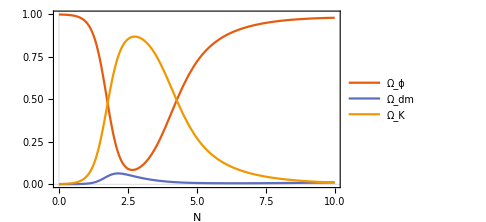

```mathematica
Plot[{(fx[t])^2+(fy[t])^2,(fs[t])^2,1-((fx[t])^2+(fy[t])^2+(fs[t])^2)},{t,0,10},PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{Style["Ω_ϕ",FontSize->18],Style["Ω_dm",FontSize->18],Style["Ω_K",FontSize->18]},LegendFunction->(Framed[#,RoundingRadius->5,FrameStyle->{Gray,Thin}]&),LegendMargins->5],{After,Top}],FrameLabel->{Style["N",FontSize->20,FontWeight->Bold],None},FrameTicksStyle->15,ImageSize->Medium]
```

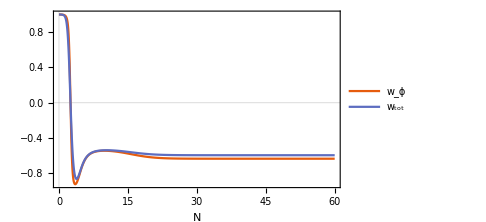

```mathematica
Plot[{((fx[t])^2-(fy[t])^2)/((fx[t])^2+(fy[t])^2),((fx[t])^2-(fy[t])^2)/((fx[t])^2+(fy[t])^2+(fs[t])^2)},{t,0,60},PlotTheme->"Scientific",PlotLegends->Placed[LineLegend[{Style["w_ϕ",FontSize->18],Style["w_tot",FontSize->18]},LegendFunction->(Framed[#,RoundingRadius->5,FrameStyle->{Gray,Thin}]&),LegendMargins->5],{Right,Top}],FrameLabel->{Style["N",FontSize->20,FontWeight->Bold],None},FrameTicksStyle->15,PlotRange->All,ImageSize->Medium]
```

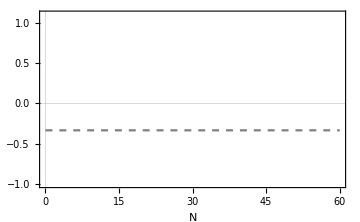

```mathematica
Plot[-1/3,{t,0,60},PlotStyle->{Dashed,Gray},PlotTheme->"Scientific",PlotRange->{-1,1+1/10},FrameLabel->{Style["N",FontSize->20,FontWeight->Bold],None},FrameTicksStyle->15,ImageSize->Medium]
```

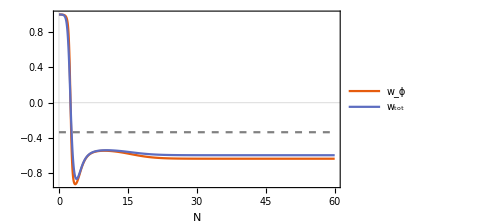

```mathematica
Show[{%144,%145}]
```